# Mathematica Quick Start

Tomás de Camino Beck, Ph.D.

## Gráficos

Para los gráficos se utiliza el comando Plot.  Para graficar la función √x, por ejemplo

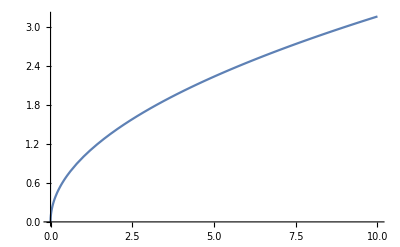

```mathematica
Plot[Sqrt[x],{x,0,10}]
```

El ejemplo muestra el gráfico para los valores de x desde 0 a 10, que se indican entre corchetes “{x, 0, 10}”. Por ejemplo el polinomio x^5+ 3 x^3-3:

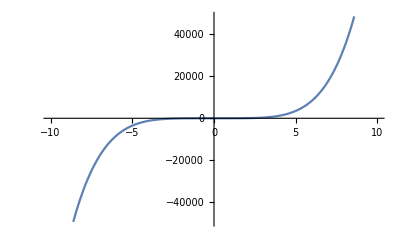

```mathematica
Plot[x^5+ 3 x^3-3,{x,-10,10}]
```

## Cálculo de Límites

Por ejemplo calculemos el límite de (x-1)/(x^2-1) cuando x→1 (Ejemplo 1 sección 2.2)

```mathematica
Limit[(x-1)/(x^2-1),x->1]
```

1/2

Para hacerlo numéricamente por la derecha

```mathematica
Table[(x-1)/(x^2-1),{x,1.5,1,-0.01}]//TableForm
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

0.4
0.401606
0.403226
0.404858
0.406504
0.408163
0.409836
0.411523
0.413223
0.414938
0.416667
0.41841
0.420168
0.421941
0.423729
0.425532
0.42735
0.429185
0.431034
0.4329
0.434783
0.436681
0.438596
0.440529
0.442478
0.444444
0.446429
0.44843
0.45045
0.452489
0.454545
0.456621
0.458716
0.460829
0.462963
0.465116
0.46729
0.469484
0.471698
0.473934
0.47619
0.478469
0.480769
0.483092
0.485437
0.487805
0.490196
0.492611
0.49505
0.497512
Indeterminate

por la izquierda

```mathematica
Table[(x - 1)/(x^2 - 1), {x, 0, 1, 0.01}] // TableForm
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

1.
0.990099
0.980392
0.970874
0.961538
0.952381
0.943396
0.934579
0.925926
0.917431
0.909091
0.900901
0.892857
0.884956
0.877193
0.869565
0.862069
0.854701
0.847458
0.840336
0.833333
0.826446
0.819672
0.813008
0.806452
0.8
0.793651
0.787402
0.78125
0.775194
0.769231
0.763359
0.757576
0.75188
0.746269
0.740741
0.735294
0.729927
0.724638
0.719424
0.714286
0.70922
0.704225
0.699301
0.694444
0.689655
0.684932
0.680272
0.675676
0.671141
0.666667
0.662252
0.657895
0.653595
0.649351
0.645161
0.641026
0.636943
0.632911
0.628931
0.625
0.621118
0.617284
0.613497
0.609756
0.606061
0.60241
0.598802
0.595238
0.591716
0.588235
0.584795
0.581395
0.578035
0.574713
0.571429
0.568182
0.564972
0.561798
0.558659
0.555556
0.552486
0.549451
0.546448
0.543478
0.540541
0.537634
0.534759
0.531915
0.529101
0.526316
0.52356
0.520833
0.518135
0.515464
0.512821
0.510204
0.507614
0.505051
0.502513
Indeterminate